# Choice of Nodes and Interpolation.

This demonstration shows the interpolating polynomial and the function for some explicit examples.

```mathematica
f[x_] := 1/(1 + (10*x)^2);
```

Functions of this form are called Runge Functions as the mathematician Runge was the first to study this issue with interpolating polynomials.

Let’s set our interval and number of nodes to take.

```mathematica
a = -1;
b =    1;
n  =   40;

EqualNodes := Table[{a + (b-a)i/n,f[a+(b-a)i/n]},{i,0,n}]
ChebyNodes := Table[{(1/2)*(a + b) + (1/2)(b-a)Cos[(2i+1)Pi/(2n+2)],
f[(1/2)*(a + b) + (1/2)(b-a)Cos[(2i+1)Pi/(2n+2)] ]},{i,0,n}]

EqP := InterpolatingPolynomial[EqualNodes,x];
ChebyP := InterpolatingPolynomial[ChebyNodes,x];
```

We now show plots of the interpolating polynomials constructed on each set of nodes, together with the original function. Here's the equally-spaced nodes interpolating polynomial:

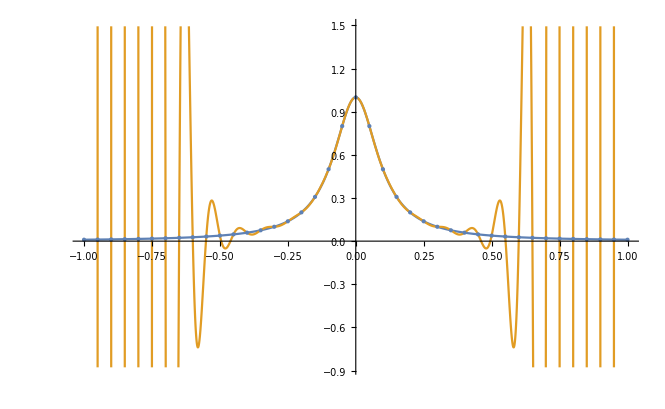

```mathematica
Show[Plot[{f[x],EqP},{x,a,b}],ListPlot[EqualNodes,PlotStyle->{PointSize[Large]}]]
```

Now we're going to see the interpolating polynomial constructed on the Chebyshev nodes:

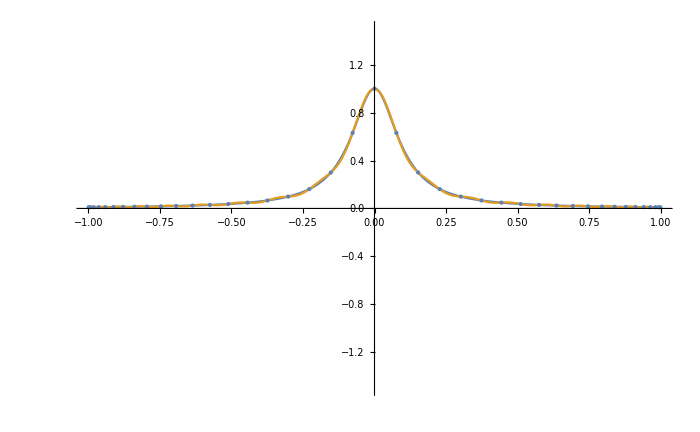

```mathematica
Show[Plot[{f[x],ChebyP},{x,a,b},PlotRange->1.5],ListPlot[ChebyNodes,PlotStyle->{PointSize[Large]}]]
```

This is so striking that we plot it again just to see some error!

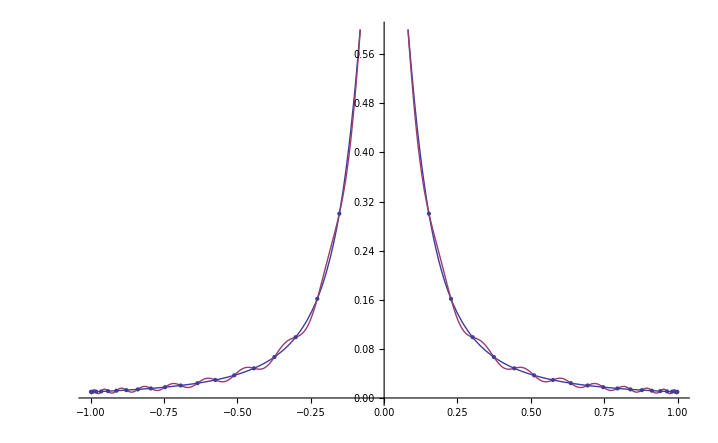

```mathematica
Show[Plot[{f[x],ChebyP},{x,a,b}],ListPlot[ChebyNodes,PlotStyle->{PointSize[Large]}]]
```

Now last class we put in a substantial amount of work developing an explicit error bound for the approximation error on N nodes for polynomial interpolation. It's worth evaluating that error bound explicitly for this function for various values of n to see what happens. Recall that our general error bound looks like:

| f(x) - p(x) | <= 1/(4n +1) M h^(n+1)

for evenly spaced nodes with spacing h, when M is a bound on the (n+1)-derivative of f, and in general, we have

| f(x) - p(x) | <= 1/((n +1)!)M ∏_(i=1)^n (x - x_i)

We will now evaluate the simple bound for n between 1 and 20 for our function f(x). The hard part will be getting a bound on the (n+1)st derivative of f, of course. We cheat by just sampling the (n+1)st derivative at a lot of (equally spaced) node points and taking the maximum value we find there.

```mathematica
M [n_] := Max[Table[D[f[x],{x,n+1}] /. x->(a + i(b-a)/(1000)),{i,0,1000}]];
```

```mathematica
EqualBound[n_] := (1/(4n+1)) * M[n] * ((b-a)/n)^(n+1);
```

```mathematica
Mtab = Table[N[M[i]],{i,1,20}]
```

{50.,4667.53,240000.,1.00321×10^7,3.81867×10^8,4.38925×10^10,4.032×10^12,3.24006×10^14,2.38433×10^16,3.62888×10^18,4.79002×10^20,5.71891×10^22,6.39046×10^24,1.20727×10^27,2.09228×10^29,3.32836×10^31,4.99494×10^33,1.14089×10^36,2.4329×10^38,4.7555×10^40}

```mathematica
EqualBoundTab = Table[N[Log[10,EqualBound[i]]],{i,1,20}]
```

{1.60206,2.71484,3.5619,4.26579,4.87205,5.9046,6.79058,7.5735,8.27704,9.25832,10.1428,10.9512,11.7005,12.6495,13.5343,14.3568,15.1301,16.0633,16.9452,17.7687}

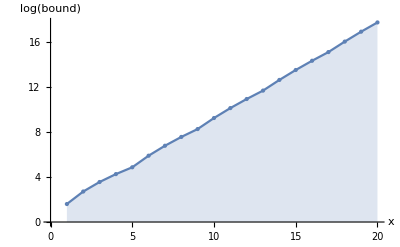

```mathematica
Show[ListLinePlot[EqualBoundTab,AxesLabel->{x,Log[bound]},Filling->Axis],ListPlot[EqualBoundTab,PlotStyle->{PointSize[Large]}]]
```

As we can see, for this function, we have the error bound (and the actual error, below it) diverging to infinity rather rapidly! For 20 evenly spaced nodes, we already have a bound on the interpolation error of something like 10^17.

We can compute the actual interpolation error as well (again, by sampling at a large number of points in the interval). It's big, but a heck of a lot smaller than the bound.

```mathematica
ActualError[n_] := Module[{Nodes,P},

	Nodes := Table[{a + (b-a)i/n,f[a+(b-a)i/n]},{i,0,n}];
  P[x_] := InterpolatingPolynomial[Nodes,x];
	Max[Table[Abs[f[N[a + i(b-a)/(1333)]] - P[N[(a + i(b-a)/(1333))]]],{i,0,1333}]]

]
ActualError[2]
ActualErrorTab = Table[ActualError[i],{i,2,20}]
```

0.810894

{0.810894,0.908291,0.614914,0.770616,0.877063,0.618017,1.84853,0.478142,4.34032,0.676211,10.8094,1.74981,27.9068,4.61259,73.7534,12.3354,198.128,33.3577,538.538}

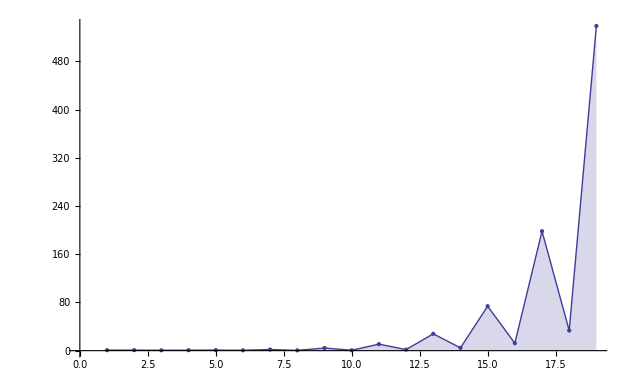

```mathematica
Show[ListLinePlot[ActualErrorTab,Filling->Axis,PlotRange->Full],ListPlot[ActualErrorTab,PlotStyle->{PointSize[Large]}]]
```

The Chebyshev error bound is still increasing, though somewhat
 slower.

```mathematica
ChebyBound[n_] := (1/(2^n*((n+1)!))) * M[n];

ChebyBoundTab = Table[N[Log[10,ChebyBound[i]]],{i,2,20}]
```

{2.28888,3.09691,3.71809,4.21943,5.13378,5.89279,6.54255,7.10833,7.94832,8.68867,9.35067,9.95173,10.7509,11.4846,12.1547,12.7747,13.5536,14.2804,14.9483}

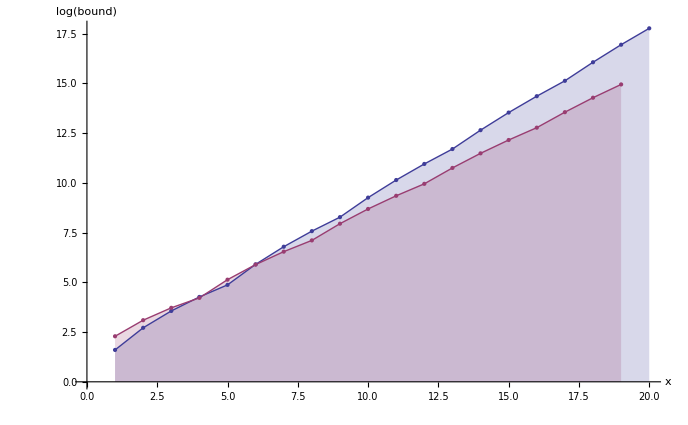

```mathematica
Show[ListLinePlot[{EqualBoundTab,ChebyBoundTab},AxesLabel->{x,Log[bound]},Filling->Axis],ListPlot[{EqualBoundTab,ChebyBoundTab},PlotStyle->{PointSize[Large]}]]
```

```mathematica
ActualChebyError[n_] := Module[{Nodes,P},
Nodes := Table[{(1/2)*(a + b) + (1/2)(b-a)Cos[(2i+1)Pi/(2n+2)],
f[(1/2)*(a + b) + (1/2)(b-a)Cos[(2i+1)Pi/(2n+2)] ]},{i,0,n}];	
  P[x_] := InterpolatingPolynomial[Nodes,x];
	Max[Table[Abs[f[N[a + i(b-a)/(1000)]] - P[N[(a + i(b-a)/(1000))]]],{i,0,1000}]]

]
ActualChebyError[2] 
ActualChebyErrorTab = Table[ActualChebyError[i],{i,2,20}]
```

0.783742

{0.783742,0.925241,0.65036,0.844002,0.537097,0.748359,0.440753,0.648873,0.359468,0.553203,0.29155,0.465879,0.235279,0.388928,0.189117,0.322716,0.151444,0.266654,0.120976}

The actual Chebyshev error is actually going down in this case (unlike the Chebyshev error bound).

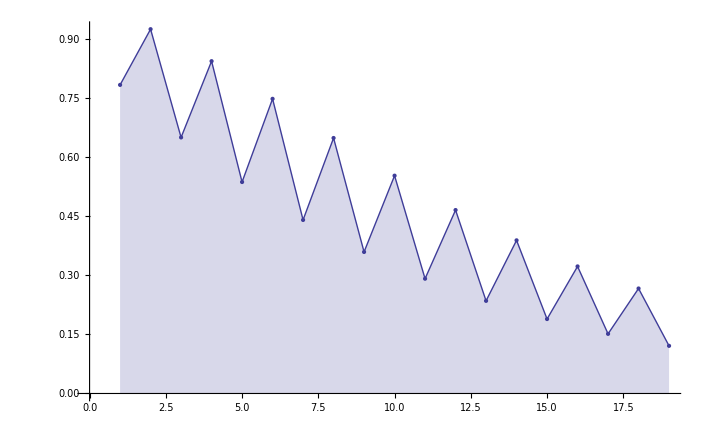

```mathematica
Show[ListLinePlot[{ActualChebyErrorTab},Filling->Axis,PlotRange->{Full},AxesOrigin->{0,0}],ListPlot[{ActualChebyErrorTab},PlotStyle->{PointSize[Large]}]]
```